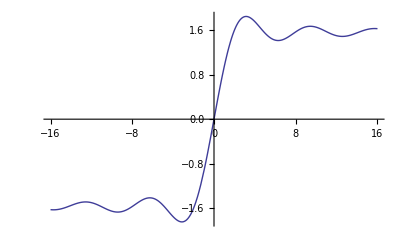

{{0,0},{1.,1.},{2.,1.84147},{3.,2.29612},{4.,2.34316},{5.,2.15396},{6.,1.96217},{7.,1.9156},{8.,2.00946},{9.,2.13313},{10.,2.17892},{11.,2.12452},{12.,2.03361},{13.,1.9889},{14.,2.02122},{15.,2.09197},{16.,2.13533}}

{{-15.,0.0433525},{-14.,0.0707577},{-13.,0.0323205},{-12.,-0.0447144},{-11.,-0.0909082},{-10.,-0.0544021},{-9.,0.0457909},{-8.,0.12367},{-7.,0.0938552},{-6.,-0.0465692},{-5.,-0.191785},{-4.,-0.189201},{-3.,0.04704},{-2.,0.454649},{-1.,0.841471},{0.,1.}}

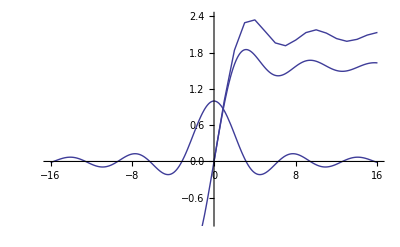

```mathematica
f[x_]=SinIntegral[x];
real=Plot[f[x],{x,-16,16}]
data=Table[{x,f[x]},{x,-16,16,.1}];
stepSize=1;
sumdx[i_]:=Sum[stepSize,{k,0,i,stepSize}]
sumdy[i_]:=N[Sum[f'[k]*stepSize,{k,0,i,stepSize}]]
euler=Prepend[Table[N[{sumdx[i],sumdy[i]}],{i,0,15,stepSize}],{0,0}]
riemann=Table[{sumdx[i],sumdy[i]},{i,0,16,stepSize}];
fake=ListLinePlot[euler];
deriv=Plot[Sin[x]/x,{x,-16,16},PlotRange->{-1,2.4}];
rightPts=Table[{k,f'[k]},{k,-15.,0}]
Show[real,fake,deriv,PlotRange->{-1,2.4}]
```

```mathematica
sumdy[2]
```

2.29612

```mathematica
f'[0]+f'[1.]+f'[2]
```

2.29612

```mathematica
f'[0]
```

1

```mathematica
sumdy[0]
```

0